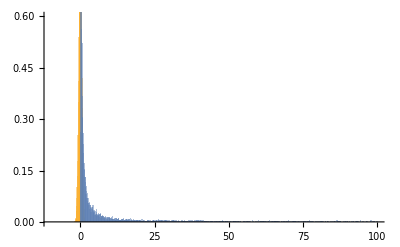

```mathematica
(* the Levy flight is investigated in detail *)
(* http://reference.wolfram.com/language/ref/LevyDistribution.html *)

(* draw 10000 values *)
dataL=RandomVariate[LevyDistribution[0,0.5],10000];
(* eliminate values bigger than 100 to make data more plotable... *)
dataL=DeleteCases[dataL,x_/;x>100];
(* compare to normal distribution *)

dataR=RandomVariate[NormalDistribution[0,0.5],10000];
Show[Histogram[{dataR,dataL},1000,"ProbabilityDensity",PlotRange->{{-10,100},{0.00,0.6}}]] (* ScalingFunctions->{"lin","log"} *)
```

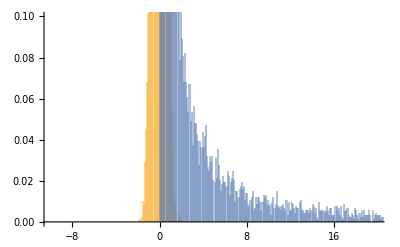

```mathematica
Show[Histogram[{dataR,dataL},1000,"ProbabilityDensity",PlotRange->{{-10,20},{0.00,0.1}}]]
```

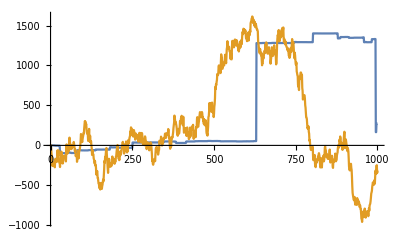

```mathematica
(* create up or down Levy steps *)
dL=RandomVariate[LevyDistribution[0.001,0.005],1000];
dLs=2*(RandomInteger[1,1000]-0.5);
dL=dL*dLs;
dR=100*RandomVariate[NormalDistribution[0,0.5],1000];
dLa=Accumulate[dL];
dRa=Accumulate[dR];
ListLinePlot[{dLa,dRa}]
```

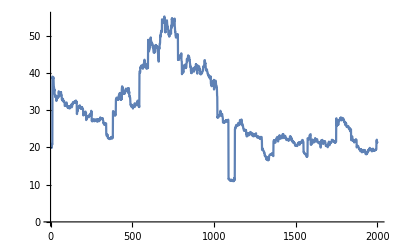

```mathematica
(* We look at a more benign form than the pure Levy flight => the stable distribution *)
dLogReturn=RandomVariate[StableDistribution[1,1.38,-0.096,-0.001,0.005],2000];
dLa=20*Exp[Accumulate[dLogReturn]];
ListLinePlot[dLa]
```

```mathematica
(* Assuming stock logarithmic return follows a stable distribution,find the value at risk at the 95% level: *)
```

```mathematica
logD=StableDistribution[1,1.38,-0.096,-0.001,0.005];
(* reference.wolfram.com/language/ref/InverseSurvivalFunction.html *)
VaR=InverseSurvivalFunction[logD,0.95]
```

-0.0186983

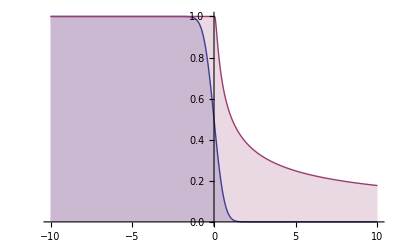

```mathematica
su1=SurvivalFunction[NormalDistribution[0,0.5]];
su2=SurvivalFunction[LevyDistribution[0,0.5]];
Plot[{su1[x],su2[x]},{x,-10,10},Filling->Axis]
```

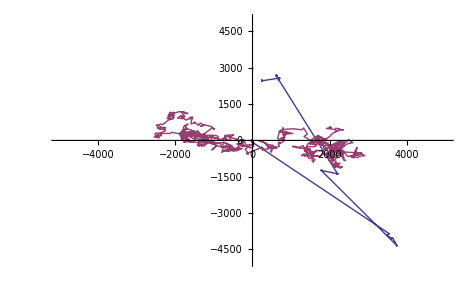

```mathematica
NN=1000;
(* create a 2D walk with Gauss and Levy *)
dLx=RandomVariate[LevyDistribution[0.0,0.005],NN];
dLx1=RandomVariate[NormalDistribution[0.0,100],NN];
dLP=RandomReal[{0,2*Pi},NN];
dLP1=RandomReal[{0,2*Pi},NN];
x={0};y={0};x1={0};y1={0};
For[j=0,j<NN,j++;dr=dLx[[j]]*Exp[I*dLP[[j]]];AppendTo[x,x[[j]]+Re[dr]];AppendTo[y,y[[j]]+Im[dr]]];
For[j=0,j<NN,j++;dr=dLx1[[j]]*Exp[I*dLP1[[j]]];AppendTo[x1,x1[[j]]+Re[dr]];AppendTo[y1,y1[[j]]+Im[dr]]];
ListLinePlot[{Transpose[{x,y}],Transpose[{x1,y1}]},PlotRange->{{-5000,+5000},{-5000,5000}}]
```